## Alzheimer’s Disease Research ADAPT In SC - Winthrop University

## Numerical Simulation of Aβ and Ca Compartments

### Parameter Choices (Arbitrary at the Moment)

```mathematica
a1 = 0.01;
a2=0.05;
b1=1000;
b2=20;
k1=0.00002617;
k2=0.1;
alph1=0.5;
alph2=0.5;
delt1=0.4;
delt2=0.4;
σ=0.00027;
r1 = k1 + (1-alph1)*delt1;
r2=k2 + (1-alph2) * delt2;
```

### Computation

```mathematica
soln=NDSolve[{ABeta'[t]==a1 - r1 * ABeta[t] + a2 * Ca[t]/(Ca[t]+σ),Ca'[t]==b1 - r2 * Ca[t] + b2*ABeta[t],ABeta[0]==0.0,Ca[0]==0.0},{ABeta,Ca},{t,0,40}];
numericalequil = NSolve[{a1 - r1 * ABeta + a2 * Ca/(Ca+σ)==0,b1 - r2 * Ca + b2*ABeta==0,ABeta>=0,Ca>=0},{ABeta,Ca}]
```

{{ABeta→0.299961,Ca→3353.33}}

```mathematica
(*values=Table[{t,ABeta[t]/. soln//First,Ca[t]/. soln//First},{t,0,40,0.1}];*)
```

```mathematica
(*values*)
```

{{0.,0.,0.},{0.1,0.00594023,98.5208},{0.2,0.011763,194.141},{0.3,0.0174704,286.947},{0.4,0.0230648,377.022},{0.5,0.0285484,464.445},{0.6,0.0339234,549.295},{0.7,0.039192,631.648},{0.8,0.0443562,711.577},{0.9,0.0494182,789.154},{1.,0.0543799,864.448},{1.1,0.0592434,937.527},{1.2,0.0640105,1008.45},{1.3,0.0686832,1077.3},{1.4,0.0732634,1144.11},{1.5,0.0777529,1208.96},{1.6,0.0821535,1271.9},{1.7,0.0864669,1333.},{1.8,0.090695,1392.29},{1.9,0.0948392,1449.84},{2.,0.0989014,1505.69},{2.1,0.102883,1559.91},{2.2,0.106786,1612.53},{2.3,0.110612,1663.6},{2.4,0.114362,1713.17},{2.5,0.118037,1761.28},{2.6,0.12164,1807.98},{2.7,0.125171,1853.3},{2.8,0.128633,1897.29},{2.9,0.132026,1939.99},{3.,0.135352,1981.44},{3.1,0.138612,2021.66},{3.2,0.141807,2060.7},{3.3,0.144939,2098.6},{3.4,0.148009,2135.38},{3.5,0.151018,2171.08},{3.6,0.153968,2205.73},{3.7,0.156859,2239.36},{3.8,0.159693,2272.},{3.9,0.162471,2303.69},{4.,0.165194,2334.44},{4.1,0.167863,2364.29},{4.2,0.170479,2393.26},{4.3,0.173043,2421.39},{4.4,0.175556,2448.68},{4.5,0.17802,2475.17},{4.6,0.180435,2500.89},{4.7,0.182802,2525.85},{4.8,0.185122,2550.08},{4.9,0.187397,2573.59},{5.,0.189626,2596.42},{5.1,0.191811,2618.57},{5.2,0.193953,2640.08},{5.3,0.196052,2660.95},{5.4,0.19811,2681.21},{5.5,0.200127,2700.88},{5.6,0.202104,2719.96},{5.7,0.204042,2738.49},{5.8,0.205941,2756.48},{5.9,0.207803,2773.93},{6.,0.209628,2790.88},{6.1,0.211417,2807.32},{6.2,0.213171,2823.29},{6.3,0.21489,2838.78},{6.4,0.216574,2853.83},{6.5,0.218226,2868.43},{6.6,0.219844,2882.6},{6.7,0.221431,2896.35},{6.8,0.222986,2909.71},{6.9,0.224511,2922.67},{7.,0.226005,2935.25},{7.1,0.227469,2947.46},{7.2,0.228905,2959.31},{7.3,0.230312,2970.82},{7.4,0.231692,2981.99},{7.5,0.233044,2992.83},{7.6,0.234369,3003.35},{7.7,0.235668,3013.57},{7.8,0.236941,3023.49},{7.9,0.238189,3033.11},{8.,0.239412,3042.45},{8.1,0.240611,3051.52},{8.2,0.241787,3060.33},{8.3,0.242939,3068.87},{8.4,0.244068,3077.17},{8.5,0.245175,3085.22},{8.6,0.24626,3093.04},{8.7,0.247323,3100.63},{8.8,0.248366,3107.99},{8.9,0.249388,3115.14},{9.,0.250389,3122.08},{9.1,0.251371,3128.82},{9.2,0.252333,3135.36},{9.3,0.253276,3141.71},{9.4,0.254201,3147.87},{9.5,0.255107,3153.86},{9.6,0.255995,3159.67},{9.7,0.256866,3165.3},{9.8,0.25772,3170.78},{9.9,0.258556,3176.09},{10.,0.259376,3181.25},{10.1,0.26018,3186.25},{10.2,0.260968,3191.11},{10.3,0.26174,3195.83},{10.4,0.262497,3200.41},{10.5,0.263239,3204.86},{10.6,0.263966,3209.18},{10.7,0.264679,3213.37},{10.8,0.265377,3217.43},{10.9,0.266062,3221.38},{11.,0.266734,3225.22},{11.1,0.267392,3228.94},{11.2,0.268037,3232.55},{11.3,0.268669,3236.06},{11.4,0.269289,3239.46},{11.5,0.269896,3242.77},{11.6,0.270491,3245.98},{11.7,0.271075,3249.09},{11.8,0.271647,3252.12},{11.9,0.272208,3255.05},{12.,0.272757,3257.9},{12.1,0.273296,3260.67},{12.2,0.273824,3263.36},{12.3,0.274342,3265.96},{12.4,0.274849,3268.5},{12.5,0.275347,3270.96},{12.6,0.275834,3273.34},{12.7,0.276312,3275.66},{12.8,0.27678,3277.91},{12.9,0.277239,3280.09},{13.,0.277689,3282.21},{13.1,0.27813,3284.27},{13.2,0.278563,3286.27},{13.3,0.278986,3288.21},{13.4,0.279402,3290.09},{13.5,0.279809,3291.92},{13.6,0.280208,3293.7},{13.7,0.280599,3295.42},{13.8,0.280983,3297.1},{13.9,0.281358,3298.72},{14.,0.281727,3300.3},{14.1,0.282088,3301.83},{14.2,0.282442,3303.32},{14.3,0.282789,3304.76},{14.4,0.283129,3306.16},{14.5,0.283462,3307.52},{14.6,0.283789,3308.85},{14.7,0.284109,3310.13},{14.8,0.284423,3311.37},{14.9,0.284731,3312.58},{15.,0.285032,3313.76},{15.1,0.285328,3314.9},{15.2,0.285618,3316.01},{15.3,0.285902,3317.08},{15.4,0.28618,3318.13},{15.5,0.286453,3319.14},{15.6,0.286721,3320.12},{15.7,0.286983,3321.08},{15.8,0.28724,3322.01},{15.9,0.287492,3322.91},{16.,0.287739,3323.78},{16.1,0.287981,3324.63},{16.2,0.288218,3325.46},{16.3,0.288451,3326.26},{16.4,0.288679,3327.04},{16.5,0.288902,3327.79},{16.6,0.289121,3328.52},{16.7,0.289336,3329.24},{16.8,0.289546,3329.93},{16.9,0.289752,3330.6},{17.,0.289955,3331.25},{17.1,0.290153,3331.88},{17.2,0.290347,3332.5},{17.3,0.290537,3333.1},{17.4,0.290724,3333.67},{17.5,0.290907,3334.24},{17.6,0.291086,3334.78},{17.7,0.291262,3335.32},{17.8,0.291434,3335.83},{17.9,0.291603,3336.33},{18.,0.291769,3336.82},{18.1,0.291931,3337.29},{18.2,0.29209,3337.75},{18.3,0.292246,3338.19},{18.4,0.292398,3338.63},{18.5,0.292548,3339.05},{18.6,0.292695,3339.45},{18.7,0.292839,3339.85},{18.8,0.29298,3340.23},{18.9,0.293118,3340.61},{19.,0.293254,3340.97},{19.1,0.293387,3341.32},{19.2,0.293517,3341.66},{19.3,0.293644,3342.},{19.4,0.293769,3342.32},{19.5,0.293892,3342.63},{19.6,0.294012,3342.94},{19.7,0.29413,3343.23},{19.8,0.294246,3343.52},{19.9,0.294359,3343.8},{20.,0.29447,3344.07},{20.1,0.294578,3344.33},{20.2,0.294685,3344.59},{20.3,0.294789,3344.84},{20.4,0.294892,3345.08},{20.5,0.294992,3345.31},{20.6,0.295091,3345.54},{20.7,0.295187,3345.76},{20.8,0.295282,3345.97},{20.9,0.295374,3346.18},{21.,0.295465,3346.38},{21.1,0.295554,3346.58},{21.2,0.295641,3346.77},{21.3,0.295727,3346.96},{21.4,0.295811,3347.14},{21.5,0.295893,3347.31},{21.6,0.295974,3347.48},{21.7,0.296053,3347.65},{21.8,0.29613,3347.81},{21.9,0.296206,3347.96},{22.,0.29628,3348.11},{22.1,0.296353,3348.26},{22.2,0.296424,3348.4},{22.3,0.296494,3348.54},{22.4,0.296563,3348.68},{22.5,0.29663,3348.81},{22.6,0.296696,3348.94},{22.7,0.296761,3349.06},{22.8,0.296824,3349.18},{22.9,0.296887,3349.3},{23.,0.296947,3349.41},{23.1,0.297007,3349.52},{23.2,0.297066,3349.63},{23.3,0.297123,3349.73},{23.4,0.297179,3349.83},{23.5,0.297234,3349.93},{23.6,0.297288,3350.02},{23.7,0.297341,3350.12},{23.8,0.297393,3350.21},{23.9,0.297444,3350.29},{24.,0.297494,3350.38},{24.1,0.297543,3350.46},{24.2,0.29759,3350.54},{24.3,0.297637,3350.62},{24.4,0.297683,3350.69},{24.5,0.297728,3350.77},{24.6,0.297773,3350.84},{24.7,0.297816,3350.91},{24.8,0.297858,3350.98},{24.9,0.2979,3351.04},{25.,0.297941,3351.11},{25.1,0.297981,3351.17},{25.2,0.29802,3351.23},{25.3,0.298059,3351.29},{25.4,0.298096,3351.34},{25.5,0.298133,3351.4},{25.6,0.298169,3351.45},{25.7,0.298205,3351.5},{25.8,0.29824,3351.55},{25.9,0.298274,3351.6},{26.,0.298307,3351.65},{26.1,0.29834,3351.7},{26.2,0.298372,3351.74},{26.3,0.298403,3351.79},{26.4,0.298434,3351.83},{26.5,0.298464,3351.87},{26.6,0.298494,3351.91},{26.7,0.298523,3351.95},{26.8,0.298552,3351.99},{26.9,0.29858,3352.02},{27.,0.298607,3352.06},{27.1,0.298634,3352.1},{27.2,0.29866,3352.13},{27.3,0.298686,3352.16},{27.4,0.298711,3352.19},{27.5,0.298736,3352.23},{27.6,0.29876,3352.26},{27.7,0.298784,3352.28},{27.8,0.298807,3352.31},{27.9,0.29883,3352.34},{28.,0.298852,3352.37},{28.1,0.298874,3352.39},{28.2,0.298896,3352.42},{28.3,0.298917,3352.45},{28.4,0.298938,3352.47},{28.5,0.298958,3352.49},{28.6,0.298978,3352.52},{28.7,0.298997,3352.54},{28.8,0.299016,3352.56},{28.9,0.299035,3352.58},{29.,0.299053,3352.6},{29.1,0.299071,3352.62},{29.2,0.299089,3352.64},{29.3,0.299106,3352.66},{29.4,0.299123,3352.68},{29.5,0.29914,3352.69},{29.6,0.299156,3352.71},{29.7,0.299172,3352.73},{29.8,0.299187,3352.74},{29.9,0.299203,3352.76},{30.,0.299218,3352.78},{30.1,0.299232,3352.79},{30.2,0.299247,3352.81},{30.3,0.299261,3352.82},{30.4,0.299275,3352.83},{30.5,0.299288,3352.85},{30.6,0.299302,3352.86},{30.7,0.299315,3352.87},{30.8,0.299328,3352.88},{30.9,0.29934,3352.9},{31.,0.299352,3352.91},{31.1,0.299365,3352.92},{31.2,0.299376,3352.93},{31.3,0.299388,3352.94},{31.4,0.299399,3352.95},{31.5,0.29941,3352.96},{31.6,0.299421,3352.97},{31.7,0.299432,3352.98},{31.8,0.299442,3352.99},{31.9,0.299453,3353.},{32.,0.299463,3353.01},{32.1,0.299473,3353.02},{32.2,0.299482,3353.02},{32.3,0.299492,3353.03},{32.4,0.299501,3353.04},{32.5,0.29951,3353.05},{32.6,0.299519,3353.06},{32.7,0.299528,3353.06},{32.8,0.299536,3353.07},{32.9,0.299545,3353.08},{33.,0.299553,3353.08},{33.1,0.299561,3353.09},{33.2,0.299569,3353.1},{33.3,0.299577,3353.1},{33.4,0.299584,3353.11},{33.5,0.299592,3353.11},{33.6,0.299599,3353.12},{33.7,0.299606,3353.13},{33.8,0.299613,3353.13},{33.9,0.29962,3353.14},{34.,0.299627,3353.14},{34.1,0.299634,3353.15},{34.2,0.29964,3353.15},{34.3,0.299646,3353.16},{34.4,0.299653,3353.16},{34.5,0.299659,3353.16},{34.6,0.299665,3353.17},{34.7,0.299671,3353.17},{34.8,0.299676,3353.18},{34.9,0.299682,3353.18},{35.,0.299687,3353.19},{35.1,0.299693,3353.19},{35.2,0.299698,3353.19},{35.3,0.299703,3353.2},{35.4,0.299708,3353.2},{35.5,0.299713,3353.2},{35.6,0.299718,3353.21},{35.7,0.299723,3353.21},{35.8,0.299728,3353.21},{35.9,0.299732,3353.22},{36.,0.299737,3353.22},{36.1,0.299741,3353.22},{36.2,0.299746,3353.22},{36.3,0.29975,3353.23},{36.4,0.299754,3353.23},{36.5,0.299758,3353.23},{36.6,0.299762,3353.23},{36.7,0.299766,3353.24},{36.8,0.29977,3353.24},{36.9,0.299774,3353.24},{37.,0.299778,3353.24},{37.1,0.299781,3353.25},{37.2,0.299785,3353.25},{37.3,0.299788,3353.25},{37.4,0.299792,3353.25},{37.5,0.299795,3353.25},{37.6,0.299798,3353.26},{37.7,0.299801,3353.26},{37.8,0.299805,3353.26},{37.9,0.299808,3353.26},{38.,0.299811,3353.26},{38.1,0.299814,3353.27},{38.2,0.299817,3353.27},{38.3,0.299819,3353.27},{38.4,0.299822,3353.27},{38.5,0.299825,3353.27},{38.6,0.299828,3353.27},{38.7,0.29983,3353.27},{38.8,0.299833,3353.28},{38.9,0.299835,3353.28},{39.,0.299838,3353.28},{39.1,0.29984,3353.28},{39.2,0.299843,3353.28},{39.3,0.299845,3353.28},{39.4,0.299847,3353.28},{39.5,0.29985,3353.28},{39.6,0.299852,3353.29},{39.7,0.299854,3353.29},{39.8,0.299856,3353.29},{39.9,0.299858,3353.29},{40.,0.29986,3353.29}}

### Visualization

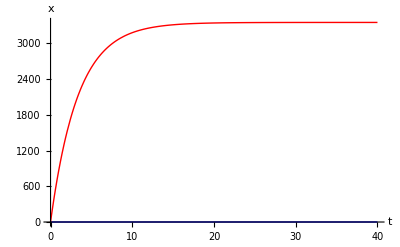

```mathematica
Plot[Evaluate[{ABeta[t],Ca[t]}/.soln],{t,0,40},PlotStyle->{{Blue,Thick},{Red,Thick}},AxesLabel->{t,x},PlotRange->All]
```

## Full Compartmental Model Simulation